```mathematica
(*plot for magnitude and direction of r having exponents from lec-4 PHY 101*)
Manipulate[Magnify[Graphics[Arrow[{{0,0},{Exp[α t],Exp[-α t]}}],PlotRange->{{-2,10},{-2,2}},Axes->True],5],{t,0,3},{α,0,1}]
```

```mathematica
(*plot of the path taken by the particle shown above*)
Manipulate[Magnify[ParametricPlot[{Exp[α t],Exp[-α t]},{t,0,T},PlotRange->{{-2,10},{-5,2}}],5],{T,0.1,2},{α,0,1}]
```

```mathematica
(*the velocity of the particle from PHY 101 lec 4*)
Manipulate[Magnify[ParametricPlot[{α Exp[α t],-α Exp[-α t]},{t,0,T},PlotRange->{{-2,10},{-5,2}}],5],{T,0.1,2},{α,0,1}]
```

```mathematica
(*the acceleration vecotor of the particle*)
Manipulate[Magnify[ParametricPlot[{a^2 Exp[a*t],a^2 Exp[-(a*t)]},{t,0,T},PlotRange->{{-2,10},{-5,2}}],5],{T,0.1,2},{a,0,1}]
```

```mathematica
(*UCM plots form lec - 5 PHY 101*)
Manipulate[Graphics[Arrow[{{0,0},{Cos[t],Sin[t]}}],PlotRange->{{-2,2},{-2,2}},Axes->True],{t,0,2*Pi}]
```

```mathematica
Manipulate[ParametricPlot[{Cos[t],Sin[t]},{t,0,T},PlotRange->{{xMin,xMax},{-2,2}}],{T,0.1,20},{xMin,-2,0},{xMax,0,2}]
```

```mathematica
(*plot of velocity vector*)
Manipulate[Graphics[{Arrow[{{Cos[t],Sin[t]},{Cos[t]-Sin[t],Sin[t]+Cos[t]}}]},PlotRange->{{-2,2},{-2,2}},Axes->True],{t,0,8}]
```

```mathematica
(*accelration*)
Manipulate[Graphics[{Arrow[{{0,0},{-Cos[t],-Sin[t]}}]},(*Acceleration vector*)PlotRange->{{-2,2},{-2,2}},Axes->True],{t,0,2*Pi}]
```

```mathematica
Plot3D[Sin[x+y],{x,1,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[y],Cos[x]},{x,-10,10},{y,-10,10}, PlotStyle->{Dashed,Blue}]
```

-Graphics3D-

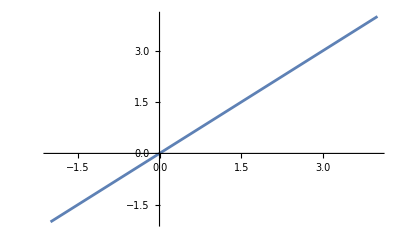

```mathematica
Plot[{x,y},{x,-2,4}]
```